# Ejercicio : Bibliografía Anotada y Programación

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Bibliografía Anotada

Classification of Sequential Sports Using Automata Theory

Este artículo analiza cómo mediante las reglas de un deporte se puede modelar los resultados ganadores mediante la definición de eventos gobernados por las reglas del mismo, este estudio se realiza sobre deportes que son considerados dentro de la categoría “Agon”, los cuales buscan mediante la competición de equipos o individuos que haya un ganador, el estudio se concentra en cómo llegar al estado final del juego el cual dicta al ganador.

Para analizar un deporte mediante este enfoque se define que todos los participantes se adhieren a un sistema de reglas y se llega a un estado final donde un ganador es anunciado. Observando las reglas de cada deporte se hace notar el hecho que hay ciertas reglas que solo aplican en momentos específicos, por ejemplo cuando la carrera ya comenzó, y que podría dejar de tener sentido al terminar el hit, por lo que los autores dividen las reglas en dos categorías: Reglas de juego y de evento, las primeras aplican durante todo el juego y las segundas sólo en ciertos eventos. Luego de tener las reglas bien definidas se debe listar los eventos que aplican dentro del deporte. Al haber terminado con estas clasificaciones los autores buscan hacer representaciones formales utilizando Autómatas de Estado Finitos.

En una máquina de estados finitos se debe capturar todos los estados posibles, todos los cambios de estados posibles y las entradas requeridas para que un sistema cambie de un estado a otro. Los autores buscan que mediante el autómata se obtenga el ganador, mediante el uso de entradas que serían la secuencia de eventos.

Antes de aplicar la metodología de los autores estos notan que en ciertos deportes hay eventos que pueden ocurrir en cualquier momento y solo si lo desean los participantes, para hacer una mejor distinción dividen los deportes en dos categorías “purposive” y estéticos, en los purposive solamente importa el ganar y no como se desarrolla el juego mientras este dentro de las reglas, los estéticos se caracterizan por ser importante la forma (normalmente son juzgados) para lograr el objetivo.

Los autores visualizan que las reglas son las que dictan el resultado de un evento, es decir el siguiente estado, los eventos siguen una secuencia lógica dictada por las reglas que aplican para el evento en los deportes purposive, los esteticos no lo siguen y no lo requieren, por lo que los autores los categorizan como Deportes no secuenciales. Por lo que los Purposive se categorizan como secuenciales y los estéticos como No secuenciales.

Los deportes secuenciales tienen un número finito de eventos, además en estos se captura la ocurrencia del evento que lleva a determinar el resultado del juego. Los autores se concentraron en este tipo de deportes para el estudio con Autómatas Finitos y determinar cómo se define un ganador.

Los autores enlistan varios estados en los que el juego puede existir, así como las reglas que son aplicables para cada evento y construyen los autómatas para cada uno, en este resumen veremos el ejemplo del deporte Shot Put.

Sistema de reglas :

Después de tomar posición los atletas deben pausar antes de tirar.
La pausa no puede ser mayor a un minuto.
El tiro no puede bajar de la altura de sus hombros
Los atletas no pueden salir del círculo hasta que el tiro sea lanzado.
El tiro debe aterrizar dentro del sector valido.

Eventos :
El atleta toma posición en la línea inicial
El atleta hace el tiro
El tiro aterriza

Mediante el sistema de reglas y los eventos definidos se definen las transiciones y estados para construir cada autómata.


Mediante los autómatas finitos podemos obtener el lenguaje regular del deporte, el cual es el set de secuencias de eventos aceptados por el deporte, sabemos que también se pueden dar estados de descalificación pero en este estudio solo se enfocan en analizar la expresión regular que lleva a determinar el ganador, por ejemplo con Shot Put tenemos inicialmente el siguiente lenguaje : 
S(R) = f | th | tsm 

Pero la expresión que nos lleva a determinar el ganador es solamente : 
S(r) = tsm

Los autores por último realizan una clasificación basados en las observaciones de las expresiones regulares :

1 - Tiempo de medición para decidir al ganador :  Las expresiones regulares que modelan estos deportes tienen en común el estado que mide el tiempo, este indica al ganador basado en el tiempo tomado por los participantes para completar la secuencia de eventos, por ejemplo Hurdles y Track.
2 - Medición de espacio :  En este caso se mide el alcance o espacio recorrido para determinar el ganador, por ejemplo el salto largo o el shot put
3 - Comparación de puntos :  En estos la expresión regular realizan una comparación de puntos, y la cantidad acumulada determina al ganador, para esta clasificación tenemos las siguientes subcategorías :
Condición ganadora : Consideraremos la expresión regular del Boliche la cual es B(r) = resf | resres | resrp2s | resrp1s | rp1sres | rp1srp2s | rp1srp1s | rp2s | rp1sf , la “s” que indica la actualización de puntaje siempre está precedida por acciones las cuales son parte de la jugada de uno de los participantes y lo hace independiente de los demás, también se observa como el puntaje se actualiza hasta llegar a la meta.
Condición perdedora : Consideraremos la expresión regular del Bádminton V(r) = lfp2 | ls(h2h1)*d2p1 | ls(h2h1)*r2p1 | ls(h2h1)*h2r1p2 | ls(h2h1)*h2d1p2
Podemos observar como “p2”, lo cual se refiere al equipo 2 siempre está precedido por una acción del equipo 1, por lo que en este deporte lo que importa es no cometer un foul ya que el equipo que lo cometa pierde el punto, las reglas no llevan a una actualización del puntaje es la condición perdedora la que define al ganador.
Condición de ganar y perder : Para este ejemplo analizaremos la expresión regular de Pacman, la cual es : P(r) = m*(es)*m*okst | m*(es)*m*(oc)*m*kst | m*(es)*m*kst | m*(es)*m* | esm*(es)*m*(oc)*m* | es(es)*m*okst | es(es)*m*(oc)*m*kst, en este caso tanto cuando un monstruo mata a pacman (k), o pacman come pac dots (e) se actualiza el puntaje, por lo que depende tanto de las acciones de pacman como de los enemigos, tanto en condición ganadora como perdedora el puntaje es actualizado.
4 - Panel de Jueces : En este tipo los jugadores solo se adhieren a las reglas y los jueces se encargan de puntuar, por ejemplo podemos analizar el levantamiento de pesas, cuya expresión regular es W(r) = lps , los eventos que preceden a “s” el cual es la actualización de puntaje son solamente el levantamiento de las barras (l) y el bajarlas (p), estos eventos no tienen mayor variedad en la forma o el orden que se realizan, la forma y técnica con que lo hagan es juzgada por el panel de jueces.

En conclusión los autores hacen distintas clasificaciones de los deportes tanto como de tipo como de conclusiones ganadoras para los mismos, a estas conclusiones se llegó gracias al modelado por autómatas finitos.

## Código / Shot Put

Construimos la función δ

```mathematica
δ = Association[
{s,"f"}-> d,
{s,"t"}-> a,
{a,"h"}-> d,
{a,"s"}-> b,
{b,"m"}-> f
]
```

<|{s,f}→d,{s,t}→a,{a,h}→d,{a,s}→b,{b,m}→f|>

```mathematica
DeltaHat[δ_,q0_,string_]:=FoldList[δ[{#1,#2}]&,q0,Characters[string]]
```

```mathematica
DeltaHat[δ,s,"tsm"]
```

{s,a,b,f}

```mathematica
IsValid[δ_,q0_,qf_List,string_]:=MemberQ[qf,Fold[δ[{#1,#2}]&,q0,Characters[string]]];
```

```mathematica
IsValid[δ,s,{d,f},"tsm"]
```

True

## ¿Qué Strings acepta?

```mathematica
testset=StringJoin /@Subsets[{"f","t", "h", "s", "m"}, {1, 3}]
```

{f,t,h,s,m,ft,fh,fs,fm,th,ts,tm,hs,hm,sm,fth,fts,ftm,fhs,fhm,fsm,ths,thm,tsm,hsm}

```mathematica
testset⟦Flatten[Position[IsValid[δ,s,{d,f},#]&/@testset, True]]⟧//TableForm
```

f
th
tsm

```mathematica
ShowGraphDFA[δ_,states_List,q0_,q_List]:=Graph[
MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}],
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
EdgeWeight->Last/@Keys[δ],
EdgeLabels->"EdgeWeight",
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]]
]
```

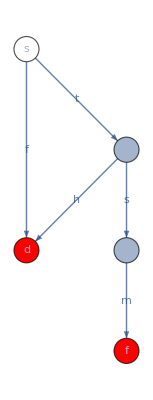

```mathematica
ShowGraphDFA[δ,{s,d,a,b,f},s,{d,f}]
```

## Código / Hurdles

```mathematica
δ = Association[
{s,"f"}-> {d},
{s,"r"}-> {a},
{a,"u"}-> {d},
{a,"v"}-> {b},
{b,"r"}-> {c, a},
{c,"m"}-> {f}
]
```

<|{s,f}→{d},{s,r}→{a},{a,u}→{d},{a,v}→{b},{b,r}→{c,a},{c,m}→{f}|>

```mathematica
DeltaHatNFA[δ_,q0_List,string_]:=FoldList[Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]&,q0,Characters[string]]
```

```mathematica
DeltaHatNFA[δ,{s},"rvrvrvrvrm"]
```

{{s},{a},{b},{a,c},{b},{a,c},{b},{a,c},{b},{a,c},{f}}

```mathematica
IsValidAFN[δ_, q0_List, qf_List, string_] := Intersection[Last[DeltaHatNFA[δ, q0, string]], qf] ≠  {}
```

```mathematica
IsValidAFN[δ, {s}, {d, f}, "rvrvrvrvrm"]
```

True

## ¿Qué Strings acepta?

```mathematica
testsetHurdles={"f","rvr", "rvrm", "rvrvrm", "rvru", "rvrvrvru", "rvrvrvrvrm","rvrvvvvm"}
```

{f,rvr,rvrm,rvrvrm,rvru,rvrvrvru,rvrvrvrvrm,rvrvvvvm}

```mathematica
testsetHurdles⟦Flatten[Position[IsValidAFN[δ,{s},{d,f},#]&/@testsetHurdles, True]]⟧//TableForm
```

f
rvrm
rvrvrm
rvru
rvrvrvru
rvrvrvrvrm

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.6,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{q0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

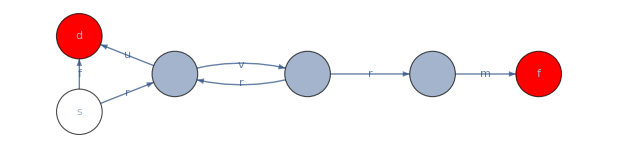

```mathematica
ShowGraphFA[{s->d,s->a,a->d, a->b,b -> a, b->c, c->f},{s,a,b, c, d, f},s,{d,f},{"f","r","u", "v", "r","r", "m"}]
```